# Sesión 3: Evolución temporal ,operadores de medición y funciones auxiliares

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
<<Wolfram`QuantumFramework`
```

## QuantumEvolve

Forma en desuso de hallar el operador unitario de evolución

```mathematica
QuantumOperator["X","ParameterSpec"->t]["EvolutionOperator"]
```

Cos[t]00-ⅈ Sin[t]01-ⅈ Sin[t]10+Cos[t]11

Lo mismo con QuantumEvolve

```mathematica
U =QuantumEvolve[QuantumOperator["X"],None,t]
```

Cos[t]00-ⅈ Sin[t]01-ⅈ Sin[t]10+Cos[t]11

Equivalente usando matrices ya que es independiente del tiempo

```mathematica
MatrixExp[-ⅈ t PauliMatrix[1]]
```

{{Cos[t],-ⅈ Sin[t]},{-ⅈ Sin[t],Cos[t]}}

Evoluciona  directamente un estado

```mathematica
QuantumEvolve[QuantumOperator["X"],QuantumState["+"],tx]//Simplify
```

(cos(tx)-ⅈ sin(tx))/(√2)0+(cos(tx)-ⅈ sin(tx))/(√2)1

Define un Hamiltoniano dependiente del tiempo y un estado inicial

```mathematica
h=Subscript[ω, 1]/2 Cos[α]QuantumOperator["Z"]+Subscript[ω, 1]/2 Sin[α](Cos[ω t]QuantumOperator["X"]+Sin[ω t]QuantumOperator["Y"]);
```

```mathematica
ψi=QuantumState[{Cos[α/2],Sin[α/2]}];
```

Evolución simbólica dependiente del tiempo, simplifica el estado final

```mathematica
ψf=QuantumEvolve[h,ψi,t];
```

```mathematica
FullSimplify[Normal[ψf["StateVector"]]]/.{√_->λ,1/√_->1/ λ}
```

{ⅇ^(-1/2 ⅈ t ω) Cos[α/2] (Cosh[(t λ)/2]+(ⅈ Sinh[(t λ)/2] (ω-ω_1))/λ),ⅇ^((ⅈ t ω)/2) Sin[α/2] (Cosh[(t λ)/2]-(ⅈ Sinh[(t λ)/2] (ω+ω_1))/λ)}

Simbolicamente no siempre es posible encontrar una solución

```mathematica
QuantumEvolve[1/2 Subscript[ω, 0] QuantumOperator["Z"]+γ Cos[Subscript[ω, p] t]QuantumOperator["X"],t]
```

QuantumEvolve::error: Differential Solver failed to find a solution

DSolveValue[{s'[t]=={{-(ⅈ ω_0)/2,-1/2 ⅈ ⅇ^(-ⅈ t ω_p) γ-1/2 ⅈ ⅇ^(ⅈ t ω_p) γ},{-1/2 ⅈ ⅇ^(-ⅈ t ω_p) γ-1/2 ⅈ ⅇ^(ⅈ t ω_p) γ,(ⅈ ω_0)/2}}.s[t],s[0]=={1,0}},s[t]∈Vectors[2,ℂ],t,{}]

Evolución númerica de estados

```mathematica
ψf = QuantumEvolve[1/2 0.3QuantumOperator["Z"]+0.7 Cos[0.4 t]QuantumOperator["X"],{t,0,5}]
```

InterpolatingFunction[…](t)0+InterpolatingFunction[…](t)1

```mathematica
ψf[4.5]
```

(-0.24208-0.194429 ⅈ)0+(0.263538-0.913317 ⅈ)1

Hallar U numéricamente

```mathematica
U =QuantumEvolve[1/2 0.3QuantumOperator["Z"]+0.7 Cos[0.4 t]QuantumOperator["X"],None,{t,0,5}]
```

QuantumOperator[…]

```mathematica
U[0]
```

(1.+0. ⅈ)00+(1.+0. ⅈ)11

```mathematica
U[0.3][QuantumState["+"]]
```

(0.690928-0.178582 ⅈ)0+(0.690944-0.115429 ⅈ)1

Devolver las ecuaciones y resolverlas explicitamente cuando se necesita un control mayor del solver numérico

```mathematica
eqns =QuantumEvolve[1/2 0.3QuantumOperator["Z"]+0.7 Cos[0.4 t]QuantumOperator["X"],None,{t,0,5},"ReturnEquations"->True]
```

{{s'[t]==SparseArray[…].s[t],s[0]==SparseArray[…]},s,{t,0,5}}

```mathematica
Unum =s/.NDSolve[Sequence@@(eqns /.l_SparseArray:>Normal[l]),Method->"ImplicitRungeKutta"][[1]]
```

InterpolatingFunction[…]

```mathematica
Unum[0.3].QuantumState["+"]["AmplitudeList"]
```

{0.690926-0.178581 ⅈ,0.690941-0.115428 ⅈ}

## Ejemplos adicionales de QuantumEvolve

### Pulso Gaussiano “Chirped”

```mathematica
Hchirped =QuantumOperator[1/2 Ω0 ⅇ^(-(t)^2 / τ^2)(Cos[κ t^2]QuantumOperator["X"]+Sin[κ t^2]QuantumOperator["Y"]),"Parameters"->{Ω0,τ,κ}];
```

```mathematica
U = QuantumEvolve[Hchirped[1.,1.,10.],None,{t,-3,3}];
```

```mathematica
ψ = U[QuantumState["+"]];
```

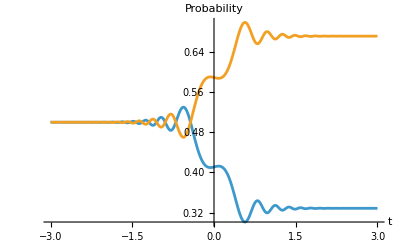

```mathematica
Plot[Evaluate@ψ[t]["ProbabilityList"],{t,-3,3},PlotRange->All,AxesLabel->{"t","Probability"},LabelStyle->13]
```

```mathematica
U = QuantumEvolve[Hchirped[25.,30.,15.],None,{t,-3,3}];
```

```mathematica
ψ = U[QuantumState["0"]];
```

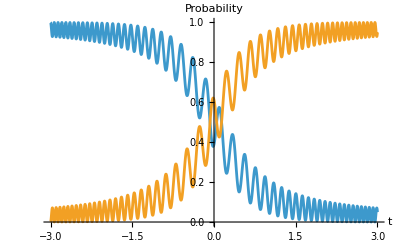

```mathematica
Plot[Evaluate@ψ[t]["ProbabilityList"],{t,-3,3},PlotRange->All,AxesLabel->{"t","Probability"},LabelStyle->13]
```

### Evolución de las componentes del vector de Bloch

```mathematica
hamiltonian=ω0 QuantumOperator["JZ"]+ 2ωp Cos[ω0 t]QuantumOperator["JX"];
```

```mathematica
ω0=2π ;ωp=π/10;
tf=2π/ωp;
```

```mathematica
r1=QuantumEvolve[hamiltonian,{t,0,tf}];
```

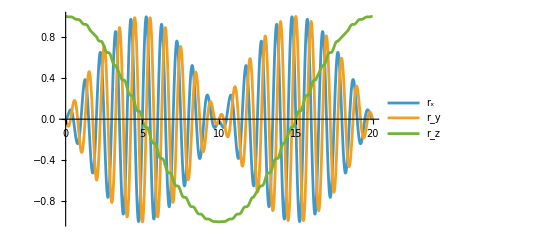

```mathematica
Plot[Evaluate@Re@r1[t]["BlochVector"],{t,0,tf},PlotRange->All,PlotLegends->{"r_x","r_y","r_z"}]
```

### Decoherencia de un qubit

```mathematica
Ω=50;γ=1;n=3;
```

```mathematica
ρ0=QuantumState[{Cos[π/8],Exp[ⅈ π/4]Sin[π/8]}]
```

cos(π/8)0+ⅇ^((ⅈ π)/4) sin(π/8)1

```mathematica
H=Ω/2 QuantumOperator["Z"];
Ls=QuantumOperator/@{"J-","J+"};
γs=γ{n+1,n};
```

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,1}]
```

QuantumState[…]

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ParametricPlot3D[Evaluate@Re@ρt[t]["BlochVector"],{t,0,1}]]
```

-Graphics3D-

### Evolución simbólica de relajación T_1,T_2 para un qubit

Define los jump operators

```mathematica
Ls={√(1/T1)QuantumOperator["J+"],√(1/T1)QuantumOperator["J-"],√(1/T2)QuantumOperator["JZ"]}
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

Computa la matriz densidad

```mathematica
ρi =QuantumState[Array[ρ,{2,2}]]
```

QuantumState[…]

```mathematica
$Assumptions=T1>0&&T2>0&&Ω0>0;
```

```mathematica
FullSimplify/@Normal[QuantumEvolve[Ω0 QuantumOperator["JZ"],Ls,ρi,t]["Computational"]["DensityMatrix"]]//MatrixForm
```

(1/2 (ρ[1,1]+ⅇ^(-(2 t)/T1) (ρ[1,1]-ρ[2,2])+ρ[2,2]) | ⅇ^(t (-1/T1-1/(2 T2)-ⅈ Ω0)) ρ[1,2]
ⅇ^(t (-1/T1-1/(2 T2)+ⅈ Ω0)) ρ[2,1] | 1/2 (ρ[1,1]+ρ[2,2]+ⅇ^(-(2 t)/T1) (-ρ[1,1]+ρ[2,2])))

Otra forma

```mathematica
Ls={QuantumOperator["J+"],QuantumOperator["J-"],QuantumOperator["JZ"]};
vals = {1/T1,1/T1,1/T2};
```

```mathematica
(FullSimplify[QuantumEvolve[Ω0 QuantumOperator["JZ"],Ls->vals,ρi,t]["Computational"]]["Table"])
```

| 1
00 | 1/2 (ρ[1,1]+ⅇ^(-(2 t)/T1) (ρ[1,1]-ρ[2,2])+ρ[2,2])
01 | ⅇ^(t (-1/T1-1/(2 T2)-ⅈ Ω0)) ρ[1,2]
10 | ⅇ^(t (-1/T1-1/(2 T2)+ⅈ Ω0)) ρ[2,1]
11 | 1/2 (ρ[1,1]+ρ[2,2]+ⅇ^(-(2 t)/T1) (-ρ[1,1]+ρ[2,2]))

## QuantumMeasurementOperator

### Mediciones proyectivas

Otra forma

```mathematica
qmo =QuantumMeasurementOperator["Y"];
```

```mathematica
QuantumMeasurementOperator[PauliMatrix[2]]["Type"]
```

Projection

```mathematica
qmo[QuantumState["+"]]//TraditionalForm
```

<|𝓎_+→1/2,𝓎_−→1/2|>

Especifica los autovalores

```mathematica
qmo =QuantumMeasurementOperator["Bell"->{1.2,2.4,5.1,3.1}]
```

ℰ_1.2 Φ^-Φ^-+ℰ_2.4 Ψ^-Ψ^-+ℰ_5.1 Ψ^+Ψ^++ℰ_3.1 Φ^+Φ^+

```mathematica
state = QuantumState["RandomPure","Bell"]
```

(0.313401+0.311666 ⅈ)Φ^-+(0.136174+0.0214557 ⅈ)Ψ^-+(-0.591517+0.411699 ⅈ)Ψ^++(0.0783321+0.510016 ⅈ)Φ^+

```mathematica
qmo[state]["Mean"]
```

3.7543

Especifica orden y la base

```mathematica
QuantumState[Sqrt@{-1,2}]
```

ⅈ0+√2 1

```mathematica
QuantumState[Sqrt@{2,-3,-5},3]
```

√2 0+ⅈ √31+ⅈ √52

```mathematica
ψ0=QuantumTensorProduct[QuantumState[Sqrt@{-1,2}],QuantumState[Sqrt@{2,-3,-5},3]]
```

ⅈ √200-√301-√502+210+ⅈ √611+ⅈ √1012

```mathematica
QuantumMeasurementOperator["ComputationalBasis"[3],{2}]
```

ℰ_000+ℰ_111+ℰ_222

```mathematica
(QuantumMeasurementOperator["ComputationalBasis"[3],{2}]@ψ0)["Probability"]
```

<|0→1/5,1→3/10,2→1/2|>

Secuencia mediciones

```mathematica
m1=QuantumMeasurementOperator["X",{1}][QuantumState[{"RandomPure",2}]]
```

<|𝓍_+→0.145491,𝓍_−→0.854509|>

```mathematica
m2=QuantumMeasurementOperator["Y",{2}][m1]
```

<|𝓍_+𝓎_+→0.0408713,𝓍_+𝓎_−→0.10462,𝓍_−𝓎_+→0.696395,𝓍_−𝓎_−→0.158114|>

### Mediciones POVM

Medición más general especificando los respectivos operadores

```mathematica
povm={o1,o2,o3}={{{2/3,0},{0,0}},{{1/6,1/(2 √3)},{1/(2 √3),1/2}},{{1/6,-1/(2 √3)},{-1/(2 √3),1/2}}};
```

```mathematica
povm={o1,o2,o3}={{{2/3,0},{0,0}},{{0,0},{0,2/3}},{{1/3,0},{0,1/3}}}
```

{{{2/3,0},{0,0}},{{0,0},{0,2/3}},{{1/3,0},{0,1/3}}}

```mathematica
o1.o2
```

{{0,0},{0,0}}

```mathematica
o2.o3
```

{{0,0},{0,2/9}}

```mathematica
o1.o3
```

{{2/9,0},{0,0}}

```mathematica
o1.o1
```

{{4/9,0},{0,0}}

```mathematica
o2.o2
```

{{0,0},{0,4/9}}

```mathematica
o3.o3
```

{{1/9,0},{0,1/9}}

```mathematica
o1+o2+o3
```

{{1,0},{0,1}}

```mathematica
PositiveSemidefiniteMatrixQ/@povm
```

{True,True,True}

```mathematica
(Plus@@povm)==IdentityMatrix[2]
```

True

```mathematica
QuantumMeasurementOperator[povm]
```

√(2/3)ℰ_1 00+√(2/3)ℰ_2 11+1/(√3)ℰ_3 00+1/(√3)ℰ_3 11

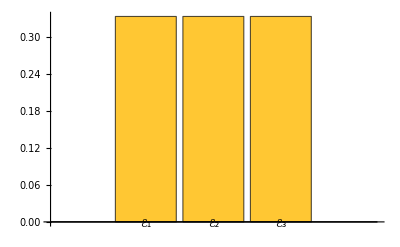

```mathematica
(QuantumMeasurementOperator[povm]@QuantumState[{1,1}])["ProbabilityPlot"]
```

```mathematica
Normal/@QuantumMeasurementOperator[povm]["POVMElements"]
```

{{{2/3,0},{0,0}},{{0,0},{0,2/3}},{{1/3,0},{0,1/3}}}

POVM nombrado

```mathematica
povm=QuantumMeasurementOperator["TetrahedronSICPOVM"]
```

QuantumMeasurementOperator[…]

```mathematica
povm[QuantumState["RandomPure"]]["Probabilities"]
```

<|𝒯_1→0.315329,𝒯_2→0.454426,𝒯_3→0.0940109,𝒯_4→0.136234|>

## Otras funciones

### QuantumPartialTrace

```mathematica
ψ = QuantumState["RandomPure",{2,3}]
```

(-0.102959+0.362513 ⅈ)00+(0.240713+0.393449 ⅈ)01+(0.301012+0.355185 ⅈ)02+(-0.311162-0.15772 ⅈ)10+(0.200464+0.264218 ⅈ)11+(-0.441984+0.0378249 ⅈ)12

```mathematica
QuantumPartialTrace[ψ,{2}]
```

(0.571525+0. ⅈ)00+(0.0074638-0.282139 ⅈ)01+(0.0074638+0.282139 ⅈ)10+(0.428475+0. ⅈ)11

```mathematica
QuantumPartialTrace[ψ,{1}]
```

(0.263714+0. ⅈ)00+(0.0137978+0.178368 ⅈ)01+(0.22933+0.22717 ⅈ)02+(0.0137978-0.178368 ⅈ)10+(0.322741+0. ⅈ)11+(0.133597-0.091427 ⅈ)12+(0.22933-0.22717 ⅈ)20+(0.133597+0.091427 ⅈ)21+(0.413545+0. ⅈ)22

### QuantumEntanglementMonotone

```mathematica
ψ = Cos[α]QuantumState["00"]+Sin[α]QuantumState["11"]
```

QuantumState[…]

```mathematica
FullSimplify[QuantumEntanglementMonotone[ψ,{{1},{2}},"Concurrence"]//ComplexExpand,0<α<π]
```

2 Abs[Cos[α]] Sin[α]

```mathematica
ψ =QuantumState[{β,0,0,Sqrt[1-β^2]},"Parameters"->β];
```

```mathematica
entanglementMetric =Table[QuantumEntanglementMonotone[ψ[α],{{1},{2}},met],{met,{"Concurrence","LogNegativity"}}]
```

{√2 Re[√(1-α^2 Conjugate[α]^2+(-1+α^2) Conjugate[√(1-α^2)]^2)],1/Log[2]Log[√((α^2 Conjugate[α/(√(Abs[α]^2+Abs[1-α^2]))]^2)/(Abs[α]^2+Abs[1-α^2]))+2 √((α √(1-α^2) Conjugate[α/(√(Abs[α]^2+Abs[1-α^2]))] Conjugate[(√(1-α^2))/(√(Abs[α]^2+Abs[1-α^2]))])/(Abs[α]^2+Abs[1-α^2]))+√(((1-α^2) Conjugate[(√(1-α^2))/(√(Abs[α]^2+Abs[1-α^2]))]^2)/(Abs[α]^2+Abs[1-α^2]))]}

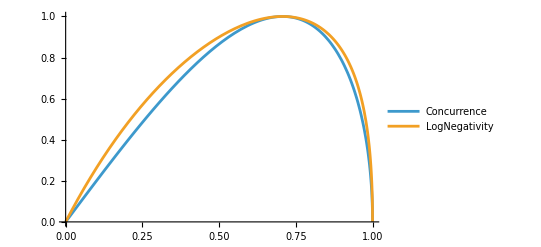

```mathematica
Plot[entanglementMetric,{α,0,1},PlotLegends->{"Concurrence","LogNegativity"}]
```

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumEntanglementMonotones
```

{Concurrence,Negativity,LogNegativity,EntanglementEntropy,RenyiEntropy,Realignment,MutualInformationI,MutualInformationJ,Discord}

### QuantumDistance

1-|ψ_pψ_σ|^2

```mathematica
QuantumDistance[QuantumState["0"],QuantumState["0"]]
```

0

```mathematica
QuantumDistance[QuantumState["0"],QuantumState["1"]]
```

1

```mathematica
QuantumDistance[QuantumState["+"],QuantumState["0"]]
```

1-1/(√2)

```mathematica
QuantumDistance[QuantumState[{{1/4,0},{0,3/4}}], QuantumState[{{1,0},{0,1}}],"Fidelity"]
```

1/2-(√3)/2

```mathematica
QuantumDistance[QuantumState["GHZ"], QuantumState["W"],"Fidelity"]
```

1

```mathematica
FullSimplify[ComplexExpand[QuantumDistance[QuantumState[{Cos[α],ⅈ Sin[α]}],QuantumState["Right"]]],0<α<π]
```

1-Abs[Cos[α]+Sin[α]]/(√2)

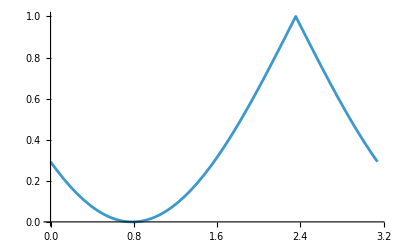

```mathematica
Plot[%,{α,0,π}]
```

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumDistances
```

{Fidelity,RelativeEntropy,RelativePurity,Trace,Bures,BuresAngle,HilbertSchmidt,Bloch}

```mathematica
QuantumDistance[QuantumState["+"],QuantumState["+"],"Bures"]
```

√2

```mathematica
QuantumDistance[QuantumState["+"],QuantumState["-"],"Bures"]
```

0

## Ejemplos extra

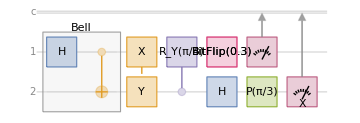

```mathematica
qc=QuantumCircuitOperator[{"Bell","XY",{"C","RY"[π/4]},"BitFlip"[.3],"H"->2,"P"[π/3]->2,{1},"M"["X"]->2}];
qc["Diagram"]
```

```mathematica
measu=qc[]
```

<|0 𝓍_+→0.307322,0 𝓍_−→0.221967,1 𝓍_+→0.192678,1 𝓍_−→0.278033|>

```mathematica
measu["Probabilities"]
```

<|0 𝓍_+→0.307322,0 𝓍_−→0.221967,1 𝓍_+→0.192678,1 𝓍_−→0.278033|>

```mathematica
%["Mean"]
```

{0.470711,0.5}

```mathematica
0*(0.3073223304703363+0.22196699141100887)+1*(0.19267766952966364+0.27803300858899116)
```

0.470711

```mathematica
1/2*(0.3073223304703363+0.19267766952966364)+1/2(0.22196699141100887+0.27803300858899116)
```

0.5